## Structural complexity of functional response models - Part 2

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/marknovak/Git/general-functional-responses/code/Mathematica

### Preliminaries

SC_2= -Log_ef(x|(Θ̂)_x)+k/2 Log_e(n/(2 π))+Log_e∫_Θ √(det I(Θ))ⅆΘ + o(1)
The first term is the likelihood. 
The second term is dependent on parameter count (k) and sample size (n).
The third term containing I(Θ), the Expected Fisher Information Matrix, reflects the model's flexibility.
The flexibility term by itself can only be compared between models having the same number of parameters.

#### Load results of "FisherMatrix-1_Compute.nb”

Pick the output that has been successfully computed :

```mathematica
Get["results/FisherMatrix-1_Output_k1"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3_NInt"];
```

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3_aNInt"];
```

### Second Term dependence on k and n

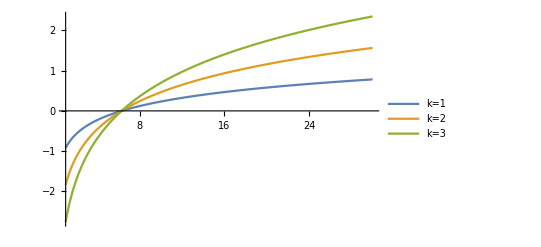
-Graphics-Sample size (n)Parameter complexity

```mathematica
AltLabel1="k";
p1=Labeled[Plot[Evaluate@Table[k/2 Log[n/(2 π)],{k,1,3}],{n,1,30},
PlotLegends->Placed[{"k=1","k=2","k=3"},Above]],
{Style["Sample size (n)"],Style["Parameter complexity"]},{Bottom,Left},
RotateLabel->True,
Spacings->{1, 0},
BaseStyle->{FontFamily->"Arial",12},
LabelStyle->{FontFamily->"Arial"},
ImageSize->Medium]
Export["results/FisherMatrix-2_Output_ParameterComplexity.pdf",p1];
```

### Third term - Flexibility

```mathematica
Labels={"H1","R","HV","H2","AG","BD","CM","AA"};
NInts={NIntH1,NIntR,NIntHV,NIntH2,NIntAG,NIntBD,NIntCM,NIntAA}
gNInts={NInts[[{1,2}]],
NInts[[{3,4,5}]],
NInts[[{6,7,8}]]
};
rNInts={NInts[[{1,2}]]/NInts[[1]],
NInts[[{3,4,5}]]/NInts[[3]],
NInts[[{6,7,8}]]/NInts[[6]]
};
(* Export["results/FisherMatrix-2_Output_logNIntegrals.txt",{Νvals,Pvals,Labels,NInts,rNInts}]; *)
```

{3.52267,2.77063,5.1177,4.80758,3.63257,4.6637,5.02265,5.60306}

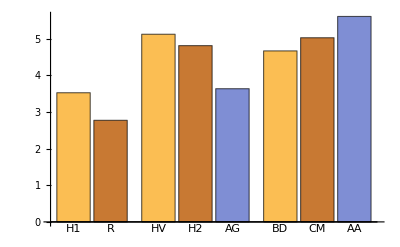
-Graphics-ModelFlexibility

```mathematica
AltLabel2="LN∫_Θ √(det  I (θ))ⅆθ";
lNInts=TakeList[MapIndexed[Labeled[#,Labels[[#2[[1]]]]]&,Flatten@gNInts],Length/@gNInts];
bc1=Labeled[BarChart[lNInts],
{Style["Model"],Style["Flexibility"]},{Bottom,Left},
RotateLabel->True,
Spacings->{0.4, 1},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"},
ImageSize->Medium]
Export["results/FisherMatrix-2_Output_Complexity_absolute.pdf",bc1];
```

```mathematica
(*
Manipulate[
ParmRange={{a,amin,amax},{h,hmin,hmax},{γ,γmin,γmax},{m,mmin,mmax},{β,βmin,βmax}};
NInts={
Log[NIntegrate[Sqrt[DetH1],ParmRange[[1]]]],
Log[NIntegrate[Sqrt[DetH2],ParmRange[[1]],ParmRange[[2]]]],
Log[NIntegrate[Sqrt[DetBD],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]]]],
Log[NIntegrate[Sqrt[DetCM],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]]]],
Log[NIntegrate[Sqrt[DetR],ParmRange[[1]]]],
Log[NIntegrate[Sqrt[DetHV],ParmRange[[1]],ParmRange[[4]]]],
Log[NIntegrate[Sqrt[DetAG],ParmRange[[1]],ParmRange[[2]]]],
Log[NIntegrate[Sqrt[DetAA],ParmRange[[1]],ParmRange[[2]],ParmRange[[4]]]]
};
BarChart[NInts/NInts[[1]],ChartLabels->{"H1","H2","BD","CM","R","HV","AG","AA"},
AxesLabel->"Complexity relative to Holling Type 1"]
,
{{amin,0.01},0.0001,.01},
{{amax,30},1,100},
{{hmin,0.01},0.0001,0.01},
{hmax,2,100},
{{γmin,0.01},0.0001,0.01},
{γmax,2,100},
{{mmin,0.01},0.0001,0.01},
{mmax,1,100}
]
*)
```

### Partial numeric Integration

Fix ' a', integrate square root of Expected Fisher Information Matrix over remaining parameters , and take natural log.

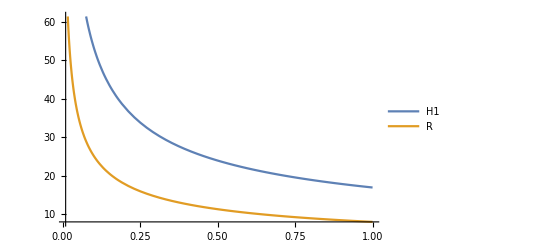

```mathematica
ParmRangeB=Drop[ParmRangeA,1];
precgoal=2;
pnk1=Plot[{
aNIntH1,
aNIntR
},
{a,0.01,1},
PlotLegends->Placed[{"H1","R"},Above]]
```

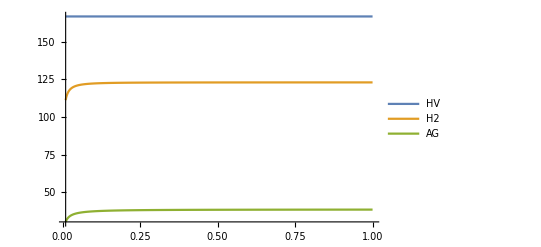

```mathematica
pnk2=Plot[{
aNIntHV,
aNIntH2[a],
aNIntAG[a]
},
{a,0.01,1},
PlotLegends->Placed[{"HV","H2","AG"},Above]]
```

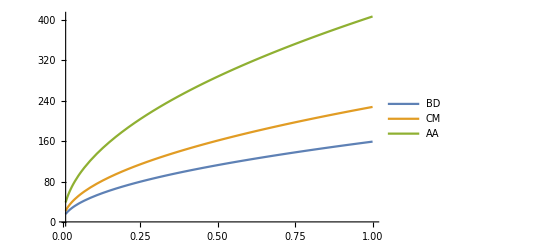

```mathematica
pnk3=Plot[{
aNIntBD[a],
aNIntCM[a],
aNIntAA[a]
},
{a,0.01,1},
PlotLegends->Placed[{"BD","CM","AA"},Above]]
```

```mathematica
pn=Labeled[GraphicsRow[{pnk1,pnk2,pnk3},ImageSize->Large],{Style["Attack rate (a)"],Style["LN∫_Θ √(det  I (θ))ⅆθ"]},{Bottom,Left},RotateLabel->True,Spacings->{3, 0},
BaseStyle->{FontFamily->"Arial",20},
LabelStyle->{FontFamily->"Arial"}]
Export["results/FisherMatrix-2_Output_partial_numeric_a.pdf",pn];
```

-Graphics-Attack rate (a)LN∫_0^θ_max √(det  I (θ))ⅆθ

Save all above result

```mathematica
Save["results/FisherMatrix-2_Ouput_PartialNumeric","`*"];
```